## Naloga 3

Sestavite funkcijo zivljenje[svet_], kot je zapisano v navodilih.

```mathematica
dodajRob[svet_]:=With[{nicle=Table[0,{Length[First[svet]]}]},Prepend[Append[#,0],0]&/@Prepend[Append[svet,nicle],nicle]]
naseljenost[svet_,n_,m_]:=Total[svet[[{n-1,n,n+1},{m-1,m,m+1}]],2]
novoStanje[svet_,n_,m_]:=If[Or[And[svet[[n,m]]==0,naseljenost[svet,n,m]==3],And[svet[[n,m]]==1,3≤naseljenost[svet,n,m]≤4]],1,0]
zivljenje[svet_]:=With[{zRobom=dodajRob[svet],n=Length[svet],m=Length[First[svet]]},Table[novoStanje[zRobom,i,j],{i,2,n+1},{j,2,m+1}]]
```

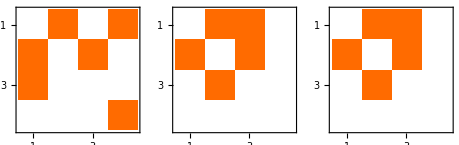

```mathematica
svet1={{0,1,0,1},{1,0,1,0},{1,0,0,0},{0,0,0,1}};
GraphicsRow[MatrixPlot/@{svet1,zivljenje[svet1],zivljenje[zivljenje[svet1]]}]
```

Ugotovite, koliko korakov je potrebno narediti, da svet dieHard izumre.

```mathematica
dieHard={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
Manipulate[MatrixPlot[Nest[zivljenje,dieHard,u]],{u,0,100,1}]
```

Svet dieHard izumre po 69 korakih.

## Naloga 4

Sestavite funkcijo krogi[l_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
seznamKrogov[{}]:=With[{d=2/(Sqrt[3]+2),r=Sqrt[3]/(Sqrt[3]+2)},Table[Circle[PolarToCartesian[{d,Pi/2+i*2*Pi/3}],r],{i,0,2}]]
seznamKrogov[l_]:=With[{d=2/(Sqrt[3]+2),r=Sqrt[3]/(Sqrt[3]+2),p=First[l]},Join[Translate[Scale[#,r,{0,0}],PolarToCartesian[{d,Pi/2+p*2*Pi/3}]]&/@seznamKrogov[Rest[l]],Table[Circle[PolarToCartesian[{d,Pi/2+i*2*Pi/3}],r],{i,0,2}]]]
krogi[l_]:=Graphics[seznamKrogov[l]]
```

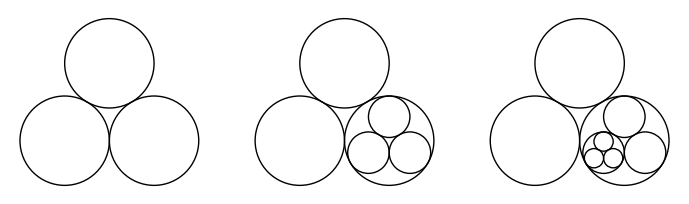

```mathematica
GraphicsRow[{krogi[{}],krogi[{2}],krogi[{2,1}]}]
```